```mathematica
WolframAlpha["Expectation[f[x]] where f[x]=x^(t^2*x)*Gamma[x]^(t^2)"]
```

WolframAlphaQueryResults

```mathematica
Solve[b^2/((a-1)^2*(a-2))==0.2^2 &&  b/(a-1)==0.01,{a,b}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{a→2.0025,b→0.010025}}

```mathematica
Solve[β==(α-1)*Esd^2 && β^2==(α-1)^2*(α-2)*m^2*Esd^2,{α,β}]
```

{{α→1,β→0},{α→(Esd^2+2 m^2)/m^2,β→(Esd^2 (Esd^2+m^2))/m^2}}

```mathematica
Expectation[TransformedDistribution[X*X,X\[Distributed]InverseGammaDistribution[α,ζ]]]
```

Expectation::argmu: Expectation called with 1 argument; 2 or more arguments are expected.

```mathematica
Expectation[x^4,x\[Distributed]InverseGammaDistribution[α,ζ]]
```

Piecewise[{{ζ^4/((-4+α) (-3+α) (-2+α) (-1+α)), α>4}, {Indeterminate, True}}]

```mathematica
Expectation[x^2,x\[Distributed]InverseGammaDistribution[α,ζ]]
```

Piecewise[{{ζ^2/((-2+α) (-1+α)), α>2}, {Indeterminate, True}}]

```mathematica
Solve[ζ==(α-1)*Esd^2 &&α/ζ^2==(m*α/ζ)^2,{α,ζ},Reals]//FullSimplify
```

{{α→0,ζ→-Esd^2},{α→1/m^2,ζ→Esd^2 (-1+1/m^2)}}

```mathematica
InverseG
```

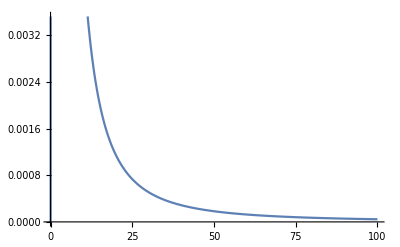

```mathematica
Plot[PDF[InverseGammaDistribution[1.02,0.5],τx],{τx,0,100}]
```

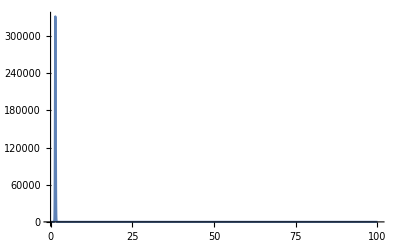

```mathematica
Plot[(x^x)*Gamma[x]^(-100),{x,0,100}]
```

```mathematica
av0=1.33;
```

```mathematica
zv0=0.081;
```

```mathematica
av0/zv0
```

16.4198

```mathematica
CDF[GammaDistribution[av0,1/zv0],2]
```

0.0682384

```mathematica
T=50;
```

```mathematica
pg[v_,αv0_,ζv0_]:=(v/2)^(T*v/2+αv0-1)*Gamma[v/2]^(-T)*Exp[(-T-2*ζv0)*v/2]
```

```mathematica
pg2[v_,αv0_,ζv0_]:=Normal[Series[pg[v,αv0,ζv0],{v,5,2}]]
```

```mathematica
lpg[v_,αv0_,ζv0_]:=(T*v/2+αv0-1)*Log[v/2]-T*LogGamma[v/2]+v/2*(-3*T/2-2*ζv0)
```

```mathematica
p[v_]:=(v/2)^(T*v/2+av0-1)*Gamma[v/2]^(-T)*Exp[(-T-2*zv0)*v/2]
```

```mathematica
lp[v_]:=(T*v/2+av0-1)*Log[v/2]-T*LogGamma[v/2]+v/2*(-T-2*zv0)
```

```mathematica
Limit[pg[v,αv0,ζv0]/(PDF[GammaDistribution[αv0,1/ζv0],v]),v->Infinity]
```

(1/ζv0)^αv0 DirectedInfinity[2^(-ⅈ Im[αv0])] Gamma[αv0]

```mathematica
Limit[pg[v,av0,zv0]/(PDF[GammaDistribution[av0,1/zv0],v]),v->Infinity]
```

0.

```mathematica
Direc
```

```mathematica
pg2[v,5,1/0.5]
```

3.33193×10^-14+1.37554×10^-13 (-5+v)+2.62453×10^-13 (-5+v)^2

```mathematica
Maximize[{lpg[v,αv0,ζv0],v>0},v]
```

Maximize[{1/2 v (-50-2 ζv0)+(-1+25 v+αv0) Log[v/2]-50 LogGamma[v/2],v>0},v]

```mathematica
Maximize[-25.081 v+(0.33000000000000007+25 v) Log[v/2]-50 LogGamma[v/2],v]
```

General::ivar: 0.000204286 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

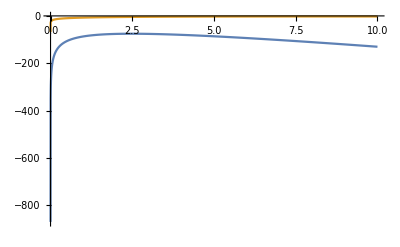

```mathematica
Plot[{lpg[v,5,0.5],Log[PDF[GammaDistribution[5,1/0.5],v]],pg2[v,5,1/0.5]},{v,0,10},PlotRange->Full]
```

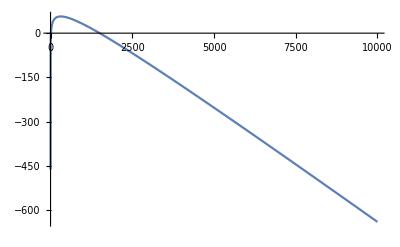

```mathematica
Plot[(T*v/2+av0-1)*Log[v/2]-T*LogGamma[v/2]+v/2*(-T-2*zv0),{v,0,10000}]
```

```mathematica
Plot[PDF[GammaDistribution[T*v/2,v/2],v]^T,{v,0,50}]
```

-Graphics-

```mathematica
Plot[((v/2)^(T*v/2+av0-1)*Gamma[v/2]^(-T)*Exp[(-T-2*zv0)*v/2])/PDF[NormalDistribution[0,1],v],{v,0,1000},PlotRange->Automatic]
```

-Graphics-

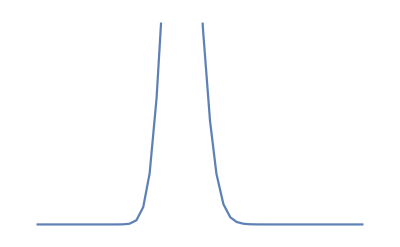

```mathematica
Show[%41,Axes->False]
```

```mathematica
NIntegrate[1/x^3,{x,0.01,Infinity}]
```

5000.

```mathematica
Expectation[x^t,x\[Distributed]GammaDistribution[v/2,v/2]]
```

(2^-t v^t Gamma[t+v/2])/Gamma[v/2]